# Teaching and learning with smart phone and Mathematica

Roger Yu

Paul Abbott

## Introduction

Mathematical literacy has become a familiar term in higher education and computational thinking as a way of communicating has also propelled its way into the main stream of our society. As a professional in the area of higher education, I am obligated to make a pathway for our students in all areas of studies to immerse themselves into this technological shift.

This project aims at combining the usages of smart phones and Wolfram language in the delivery of one of our core courses. The core course  considered here is required for all freshmen students. Approximately 30 sections of the course is offered in each semester and each section has about 30 students coming from all  disciplines ranging from engineering, sciences, math, to arts, and architecture. 

Currently, we are already using smart phones as a tool, in some cases the only tool, in hands-on activities or experiments. This project integrates Mathematica with the application of smart phones so to encourage students to make comparisons between theory and observation.

## Integration of smart phones and Mathematica

In the following, we will discuss a few examples of engaging practices that each student will work on his/her own. All of these examples can be chosen by courses at different levels or disciplines.

1) Example 1-Voice recognition and analysis

```mathematica
a=AudioCapture[]
```

```mathematica
Spectrogram[a]
```

-Graphics-

```mathematica
b=AudioLocalMeasurements[a,"Formants"]
```

TimeSeries[…]

```mathematica
AudioPlot[a]
```

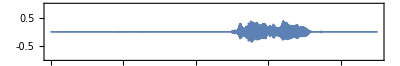

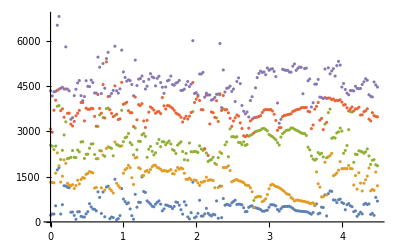

```mathematica
ListPlot[b]
```

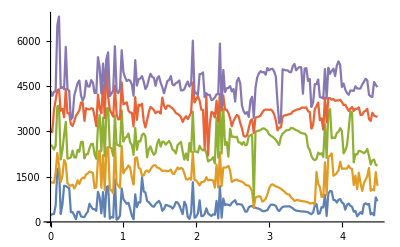

```mathematica
ListLinePlot[b]
```

```mathematica
c=AudioLocalMeasurements[a, "Max"]
```

TimeSeries[…]

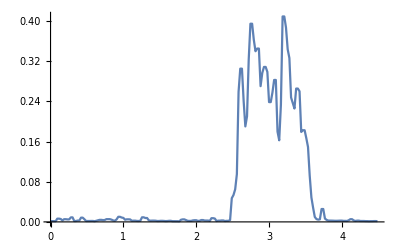

```mathematica
ListLinePlot[c]
```

### 2) Example 2-Analysis of “ExampleDada

```mathematica
aa=Audio[File["ExampleData/car.Mp3"]]
```

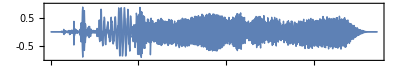

```mathematica
AudioPlot[aa]
```

```mathematica
cc=AudioLocalMeasurements[aa,"Max"]
```

TimeSeries[…]

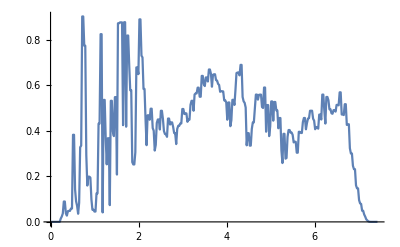

```mathematica
ListLinePlot[cc]
```

### 3) Example 3-analysis of audio signals captured by smart phone

```mathematica
aaa=Import["/Users/rogeryu/Desktop/WSS19/photoandvideo/Recording 2019-07-04 09-22-43.wav"]
```

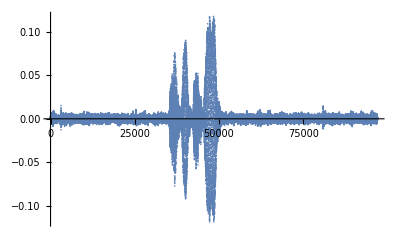

```mathematica
ListPlot[AudioData[aaa],PlotRange->All]
```

```mathematica
Manipulate[
Periodogram[aaa,width], {width,100, 8000,1},SaveDefinitions->True]
```

### 4) Example 4-Analysis of audio signals from an air tube

```mathematica
Import["/Users/rogeryu/Desktop/WSS19/photoandvideo/IMG_3601.jpg"]
```

-Graphics-

```mathematica
Import["/Users/rogeryu/Desktop/WSS19/photoandvideo/IMG_3602-1.jpg"]
```

-Graphics-

```mathematica
Import["/Users/rogeryu/Desktop/WSS19/photoandvideo/IMG_3603.jpg"]
```

-Graphics-

```mathematica
video=Import["/Users/rogeryu/Desktop/WSS19/photoandvideo/IMG_3606.TRIM.MOV","ImageList"];
```

### At this point, I don’t have a tube to work with so I can only discuss the example using photos and videos as shown above.